```mathematica
Clear[lcoo,p,lm,lpagg,lnaus,genTuCox,genPerm];
```

```mathematica
genTuCox[clr1_:Black,clr2_:Green,nfs_:0,prm_:{0},cx_:0,cy_:0]:=(
r=10;
dfs=Pi/2+Pi/30;
da=2Pi/30;
If[prm[[1]]==0,perm={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30},perm=prm];

lcoo=Range[30];
ang=0;
fs=Pi/15 nfs;
For[k=1,k≤30,k++,
pp={cx+r Cos[ang+dfs+fs],cy+r Sin[ang+dfs+fs]};
lcoo[[perm[[k]]]]=pp;
ang-=da
];

colors={"Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue","Red","Blue"};

p=Range[30];
sizep=0.005;
For[k=1,k≤30,k+=2,
p[[k]]={PointSize[sizep],RGBColor[colors[[perm[[k]]]]],Point[lcoo[[k]]]}
];
For[k=2,k≤30,k+=2,
p[[k]]={PointSize[sizep],RGBColor[colors[[perm[[k]]]]],Point[lcoo[[k]]]}
];

ln=Range[30];
For[k=1,k≤29,k++,
ln[[k]]=Line[{lcoo[[k]],lcoo[[k+1]]}]
];
ln[[30]]=Line[{lcoo[[30]],lcoo[[1]]}];

lpagg=List[{1,14},{2,19},{3,24},{4,11},{5,28},{6,15},{7,20},{8,25},{9,30},{10,17},{12,21},{13,26},{16,23},{18,27},{22,29}];
lnaus=Range[15];
For[k=1,k≤15,k++,
lnaus[[k]]=Line[{lcoo[[lpagg[[k]][[1]]]],lcoo[[lpagg[[k]][[2]]]]}]
];

Return[{p,{clr1,ln},{clr2,lnaus}}];
)

genPerm[per_,n_]:=(
result=Range[n];
nel1=Length[per];
For[k1=1,k1≤nel1,k1++,
nel2=Length[per[[k1]]];
For[k2=nel2,k2>=1,k2--,
inda=per[[k1]][[k2]];
If[k2<nel2,result[[indp]]=result[[inda]],appo=result[[inda]]];
indp=inda;
];
result[[indp]]=appo;
];
Return[result];
)
```

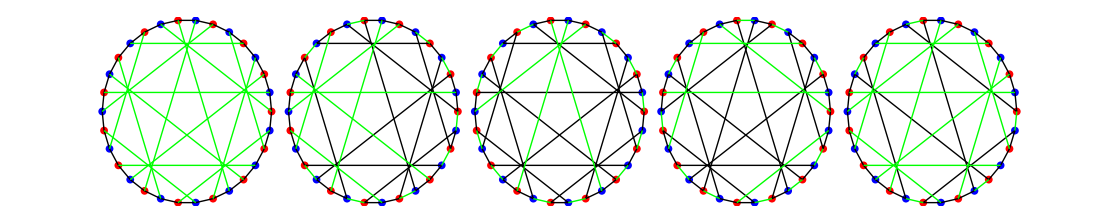

```mathematica
gen1={{5,11},{6, 10},{7, 17},{8 ,16},{9, 15},{12, 28},{13, 29},{14, 30},{18, 20},{21, 27},{22, 26},{23 ,25}};
gen2={{5,11},{6, 12},{7, 21},{8 ,22},{9, 29},{10, 28},{13, 15},{16, 26},{17, 27},{23, 25}};
gen3={{2,14},{3, 15},{4, 6},{7 ,11},{8, 10},{12, 20},{13, 19},{16, 24},{17, 25},{18, 26}};
gen4={{1,2,3, 4,5, 6,7 ,8,9, 30},{10, 29,14, 19,24, 11,28, 15,20, 25},{12, 27,16 ,21,26,17,22,13,18,23}};

g1=genTuCox[Black,Green,0];
g2=genTuCox[Black,Green,0,genPerm[gen1,30],22,0];
g3=genTuCox[Black,Green,0,genPerm[gen2,30],44,0];
g4=genTuCox[Black,Green,0,genPerm[gen3,30],66,0];
g5=genTuCox[Black,Green,0,genPerm[gen4,30],88,0];
Graphics[{g1,g2,g3,g4,g5}]
```